# Modern Physics Review

## The Special Theory of Relativity

```mathematica
(*Notes from practice:
Remember that light-years is always an x component so use the right formula.
Wavelength changes stopping potential.
	I changes with respect to current.  E = hc/lambda
Slide 9, no answers
slide 26 pauli exclusion for fermions. energy level occupied is different, bosons (spin 1) can fill the first state endlessley
*)


rdoppleraway[freq_,ratio_]:=Round[freq*Sqrt[Divide[1-ratio,1+ratio]]];
rdopplerreturn[freq_,ratio_]:=Round[freq*Sqrt[Divide[1+ratio,1-ratio]]];
rdoppleraway[5,.6]
rdopplerreturn[5,.6]
Manipulate[Show[Graphics[{Arrowheads[0.03],Red,Thick,Arrow[{{0,0},{10*Tan[0],10}}],Arrow[{{0,0},{(10-(10-g))*Tan[v1],g}}],Arrow[{{(10-(10-g))*Tan[v1],g},{(10*Tan[v1])-10*Tan[v1],g*2}}],

Table[With[{t=i},
{Blue,Thin,Arrow[{{0,t},{10,t+10}}]}],{i,-10,10}]},

PlotRange->{{0,10},{0,10}}],

Axes->True,AxesLabel->{"Distance","Time"}],{{v1,π/50,"Velocity of Event (fraction of c)"} ,0.,(85*π)/400,.1},
{{g,5,"Length of Time"},0,5,.5}
]
```

## Wave Particle Duality

```mathematica
debroglie := 3+x
```

## The Schrödinger Equation

#### Harmonic Oscillator of Ground State to Excited States

```mathematica
h=1;
V0=1;
V[x_]:= V0/2*x^2
Ham = -1/2*psi''[x]+V[x]*psi[x];
{vals,funs}=NDEigensystem[Ham, psi[x],{x,-5,5}, 8, Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions" ->{MaxCellMeasure->0.01}}}}];
vals
funs
Manipulate[
Show[
Plot[Evaluate[vals],{x,-4,4}, Frame-> True, Axes->False, PlotStyle->Directive[Dashed,Opacity[.5]]],
Plot[Evaluate[-0.7h*funs[[i]]+vals,{x,-4,4},Frame->True,Axes->False],
Plot[V[x],{x,-4,4},PlotStyle->Directive[Dashed,Black]],
PlotRange->{{-4,4},{0,8}},AxesOrigin->{-3,0},ImageSize->Medium]],
{{i,0,"Energy State Parameter"},1,8}]
```

## Models of Atoms and Electrons

```mathematica
a0=1;

ψ[{n_,l_,m_},{r_,θ_,ϕ_}]:=With[{ρ=2 r/(n a0)},Sqrt[(2/(n a0))^3 (n-l-1)!/(2 n (n+l)!)] Exp[-ρ/2] ρ^l LaguerreL[n-l-1,2 l+1,ρ] SphericalHarmonicY[l,m,θ,ϕ]]

DensityPlot3D[(Abs@ψ[{3,2,0},{Sqrt[x^2+y^2+z^2],ArcTan[z,Sqrt[x^2+y^2]],ArcTan[x,y]}])^2,{x,-10 a0,10 a0},{y,-10 a0,10 a0},{z,-15 a0,15 a0},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
a0=1;

ψ[{n_,l_,m_},{r_,θ_,ϕ_}]:=With[{ρ=2 r/(n a0)},Sqrt[(2/(n a0))^3 (n-l-1)!/(2 n (n+l)!)] Exp[-ρ/2] ρ^l LaguerreL[n-l-1,2 l+1,ρ] SphericalHarmonicY[l,m,θ,ϕ]]

DensityPlot3D[(Abs@ψ[{3,2,1},{Sqrt[x^2+y^2+z^2],ArcTan[z,Sqrt[x^2+y^2]],ArcTan[x,y]}])^2,{x,-10 a0,10 a0},{y,-10 a0,10 a0},{z,-15 a0,15 a0},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
DensityPlot3D[(Abs@ψ[{3,2,2},{Sqrt[x^2+y^2+z^2],ArcTan[z,Sqrt[x^2+y^2]],ArcTan[x,y]}])^2,{x,-10 a0,10 a0},{y,-10 a0,10 a0},{z,-15 a0,15 a0},PlotLegends->Automatic]
```

-Graphics3D-

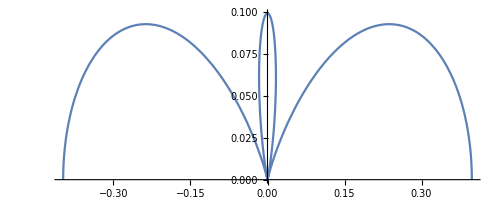

```mathematica
PolarPlot[Abs[1/4 √(5/π) (-1+3 Cos[θ]^2)]^2,{θ,0,Pi}]
```

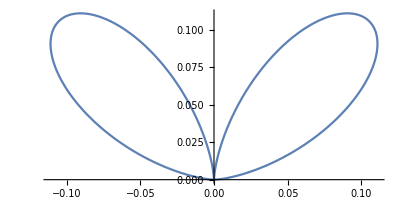

```mathematica
PolarPlot[Abs[1/2 ⅇ^(ⅈ 0) √(15/(2 π)) Cos[θ] Sin[θ]]^2,{θ,0,Pi}]
```

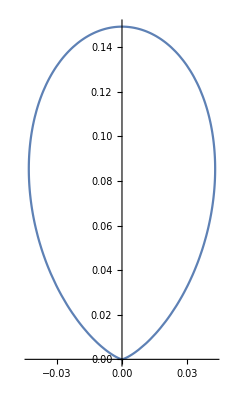

```mathematica
PolarPlot[Abs[1/4 ⅇ^(2 ⅈ 0)√(15/(2 π)) Sin[θ]^2]^2,{θ,0,Pi}]
```

## Statistical Mechanics

```mathematica
dirac=1
```

## Solid-State Physics

```mathematica
ElementData["Boron","CrystalStructureImage"]
ElementData["Boron","ElectronicConfiguration"]
```

-Graphics3D-

1s^22s^22p^1

## Nuclear Structure, Radioactivity, and Reactions

```mathematica
DSolve[{y'[x]+y[x]==a Sin[x],y[0]==0},y[x],x]
```

DSolve::dsfun: 0 cannot be used as a function.

DSolve[{(-y)[x]==a Sin[x],y[0]==0},0,x]

```mathematica
100/.20
```

500.